# Data preprocessing: Saiz et al 2020 data set NANOG, GATA6 (rat and rb antibody)

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
shiftValue[expName_,val_,threshold_,experiments_]:=Switch[expName,experiments[[1,1]],val+(threshold[[1]]-threshold[[1]]),experiments[[2,1]],val+(threshold[[1]]-threshold[[2]]),experiments[[3,1]],val+(threshold[[1]]-threshold[[3]]),experiments[[4,1]],val+(threshold[[1]]-threshold[[4]])]
```

```mathematica
zCorrection[fileName_,slope_,channels_:{"Dapi","Nanog","Gata6","Gata4"}]:=Block[{nucleiFeatures,nucleiFeaturesWithCorr,exportFName},
nucleiFeatures="NucleiFeatures"/.Import[fileName];
nucleiFeaturesWithCorr=Join[#,
Table[channels[[i]]<>"-AvgLnCorr"->Log[channels[[i]]<>"-Avg"/.#]-slope[[i]]*("Centroid"/.#)[[3]],{i,1,Length[channels]}]&@#]&/@nucleiFeatures;
exportFName=StringReplace[fileName,"Features.mx"->"Features_ZCorrected.mx"];
Export[exportFName,"NucleiFeatures"->nucleiFeaturesWithCorr]
]
```

```mathematica
fontOption="Arial";
```

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
smoothedValues[unsmoothedData_,smooth_]:=Block[{xValues,yValues,lowerLimit,mean},
xValues=#[[All,1]]&/@unsmoothedData;
yValues=#[[All,2;;3]]&/@unsmoothedData;
Table[lowerLimit=Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]&@yValues[[i]];mean=Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]];Table[Join[mean[[i]],{(mean-lowerLimit)[[i,-1]]}],{i,1,Length[mean]}],{i,1,Length[xValues]}]
]
```

```mathematica
colourNegPos[i_]:={Lighter[Gray,0.3],Darker[Gray,0.7]}[[i]]
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
colour2[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7]}[[i]]
```

```mathematica
colour1[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7],Darker[Cyan,0.5]}[[i]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Get data from NS_2020 folder

```mathematica
fNames=FileNames["*Final.mx",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"NS_2020_NG6\\FeaturesG6RbAb"}]];
```

```mathematica
CopyFile[#,StringReplace[#,"NS_2020_NG6\\FeaturesG6RbAb"->"NS_2020_NRatG6Rb\\EmbryoFeatures"]]&/@fNames
```

should be 28 files

## Unify notations

```mathematica
fileNamesRaw=FileNames["*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
RenameFile[#,StringReplace[#,".mx"->"SaizNotation.mx"]]&/@fileNamesRaw;
```

```mathematica
fNamesSaiz=FileNames["*FinalSaizNotation.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@fNamesSaiz;
```

```mathematica
nucleiFeaturesSaiz=("NucleiFeatures"/.data);
```

```mathematica
DeleteDuplicates[Flatten[StringCases[Keys[#[[1]]],"NANOG"~~___]]&/@nucleiFeaturesSaiz]
```

{{NANOG.rat-Avg,NANOG.rat-Sum,NANOG.rat-marker,NANOG.rat-ebLogCor,NANOG.rat-ebLogCor.s,NANOG.rat-AvgNorm},{NANOG.rat-Avg,NANOG.rat-Sum,NANOG.rat-marker,NANOG.rat-ebLogCor,NANOG.rat-ebLogCor.s,NANOG.rat-ebLogCor.l,NANOG.rat-AvgNorm}}

```mathematica
DeleteDuplicates[Flatten[StringCases[Keys[#[[1]]],"GATA6"~~___]]&/@nucleiFeaturesSaiz]
```

{{GATA6.rb-Avg,GATA6.rb-Sum,GATA6.rb-ebLogCor,GATA6.rb-ebLogCor.x,GATA6.rb-ebLogCor.s,GATA6.rb-ebLogCor.xs,GATA6.rb-ebLogCor.xl,GATA6.rb-AvgNorm},{GATA6.rb-Avg,GATA6.rb-Sum,GATA6.rb-ebLogCor,GATA6.rb-ebLogCor.x,GATA6.rb-ebLogCor.s,GATA6.rb-ebLogCor.xs,GATA6.rb-ebLogCor.l,GATA6.rb-ebLogCor.xl,GATA6.rb-AvgNorm}}

```mathematica
appendRules[nucleusFeatures_]:=
Join[nucleusFeatures,{"TE/ICM"->If[("Identity.hc"/.#)≠"TE","ICM","TE"],"Quadrant"->Switch[("Identity.hc"/.#),"TE","TE","DP","N+G6+","DN","N-G6-","EPI.lo","N-G6-","EPI","N+G6-","PRE","N-G6+"],"Nanog-AvgShifted"->Exp["NANOG.rat-ebLogCor"/.#],
"Gata6-AvgShifted"->Exp["GATA6.rb-ebLogCor"/.#]}&@nucleusFeatures]
```

```mathematica
Table[dataSaiz=Import[#]&@fName;
	nucleiFeatSaiz=("NucleiFeatures"/.dataSaiz);
globalFeatures=("GlobalFeatures"/.dataSaiz);
nucleiFeatures=appendRules/@nucleiFeatSaiz;
genotypeKeys=Flatten[StringCases[Keys[nucleiFeatSaiz[[1]]],"Genotype"~~___]];
staging={"Experiment"/.nucleiFeatures[[1]],"Embryo_ID"/.nucleiFeatures[[1]],"CellNumberStage"/.globalFeatures,(genotypeKeys/.nucleiFeatSaiz[[1]])};
fNameExport=StringReplace[fName,"SaizNotation.mx"->"Data.mx"];
exportData={"NucleiFeatures"->nucleiFeatures,"GlobalFeatures"->globalFeatures,"Staging"->staging};Export[fNameExport,exportData]
,{fName,fNamesSaiz}]
```

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
DeleteDuplicates/@staging[[All,-1]]
```

{{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt},{wt}}

all Wt

## Plot preprocessed data

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
Tally[staging[[All,-2]]]
```

{{3.5,11},{4.5,8},{4.,8},{3.,1}}

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
exprICM={"Nanog-AvgShifted","Gata6-AvgShifted"}/.nucleiFeaturesICM;
```

```mathematica
exprICMByStage=Table[Select[Transpose[{staging,exprICM}],#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@exprICMByStage
```

{11,8,8}

```mathematica
Length[Flatten[#[[All,2]],1]]&/@exprICMByStage
```

{265,226,269}

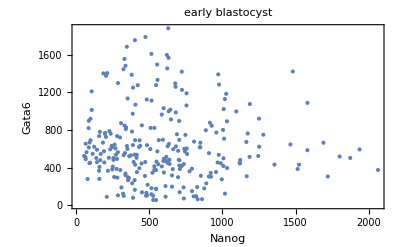
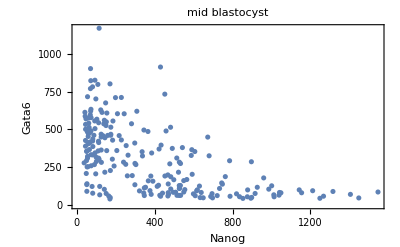
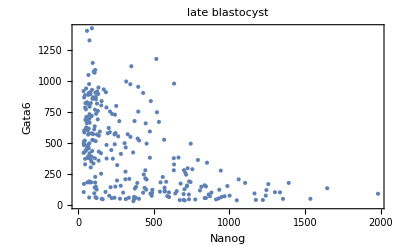
{-Graphics-,-Graphics-,-Graphics-}ICM cells

```mathematica
Labeled[Table[Show[ListPlot[#[[1;;2]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

## Plot populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N+G6+","N-G6-","N+G6-","N-G6+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,2},{N+G6+,184},{N+G6-,33},{N-G6+,46}},{{N-G6-,10},{N+G6+,52},{N+G6-,82},{N-G6+,82}},{{N-G6-,14},{N+G6+,73},{N+G6-,70},{N-G6+,112}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,2},{N+G6+,184},{N+G6-,33},{N-G6+,46}},{{N-G6-,10},{N+G6+,52},{N+G6-,82},{N-G6+,82}},{{N-G6-,14},{N+G6+,73},{N+G6-,70},{N-G6+,112}}}

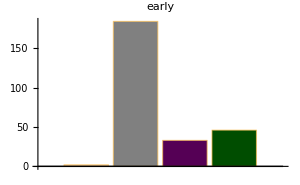
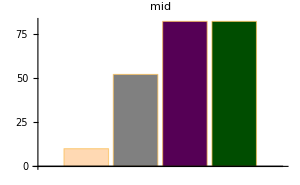
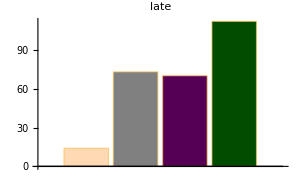

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

## ICM cells positive and negative

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
populationsICMByStage=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

#### Nanog

```mathematica
nanogPositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{27,22,29,26,21,17,20,8,12,15,20},{25,16,21,17,14,14,14,13},{18,22,17,21,24,22,12,7}}

```mathematica
Length/@nanogPositiveByStage
```

{11,8,8}

```mathematica
nanogNegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{0,0,2,2,10,8,3,5,8,1,9},{2,17,2,12,10,14,15,20},{8,12,14,14,13,7,23,35}}

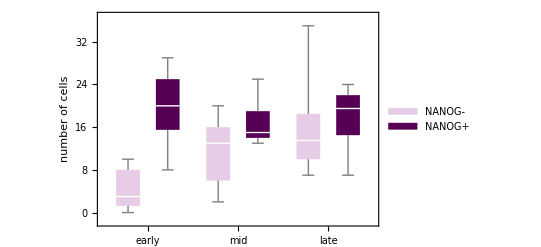

```mathematica
BoxWhiskerChart[Transpose[{nanogNegativeByStage,nanogPositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"NANOG-","NANOG+"}),ChartStyle->{Lighter[Purple,0.8],Darker[Purple]}]
```

#### Gata6

```mathematica
gata6PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{27,20,30,27,17,12,20,13,19,16,29},{12,21,18,20,11,14,16,22},{17,15,24,26,28,21,28,26}}

```mathematica
gata6NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{0,2,1,1,14,13,3,0,1,0,0},{15,12,5,9,13,14,13,11},{9,19,7,9,9,8,7,16}}

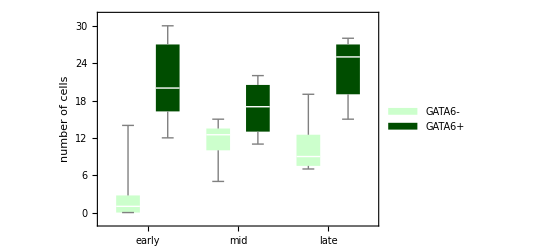

```mathematica
BoxWhiskerChart[Transpose[{gata6NegativeByStage,gata6PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA6-","GATA6+"}),ChartStyle->{Lighter[Green,0.8],Darker[Green,0.7]}]
```

#### Export

```mathematica
allCells=Transpose[{nanogNegativeByStage[[#]],nanogPositiveByStage[[#]],gata6NegativeByStage[[#]],gata6PositiveByStage[[#]]}]&/@{1,2,3};
```

```mathematica
exportList=Table[{"early","mid","late"}[[i]]->Join[{{"Our embryo data: number of positive and negative cells", "","","",DateString[]},{"ICM cells, Staging by cell number","each row represents one embryo"},{"N-","N+","G6-","G6+"}},allCells[[i]]],{i,1,3}];
```

```mathematica
(Length[#]-3)&/@exportList[[All,2]]
```

{11,8,8}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ResultsSaiz","positiveNegativeCells.xlsx"}],exportList]
```

## Calculate and export neighbour comparison files

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogNanogComp.mx"}],nanogNanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6Gata6Comp.mx"}],gata6Gata6Comp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6NanogComp.mx"}],gata6NanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogGata6Comp.mx"}],nanogGata6Comp]
```